```mathematica
(*Parameters*)
DeltaE=0.1;
DeltaA1=0.0;
epsilon0=0.01;

dvec[kx_,ky_]:={DeltaE*Sin[kx]+DeltaA1*(Cos[kx]+Cos[ky]),DeltaE*Sin[ky],-2*(Cos[kx]+Cos[ky])-epsilon0};


gradX[kx_,ky_]=D[dvec[kx,ky],kx];
gradY[kx_,ky_]=D[dvec[kx,ky],ky];


integrand[kx_,ky_]:=Module[{d,dx,dy},d=dvec[kx,ky];
dx=gradX[kx,ky];
dy=gradY[kx,ky];
Dot[d,Cross[dx,dy]]/(Norm[d]^3)];

chernDVector=(1/(4 Pi))*NIntegrate[integrand[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->5000},PrecisionGoal->3,AccuracyGoal->12,(*Tells it to stop if the value is<10^-5*)MaxPoints->1000000]; (*Give it more room to breathe*)

Print["Chern Number (d-vector way): ",chernDVector]
```

Chern Number (d-vector way): 0.9999

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

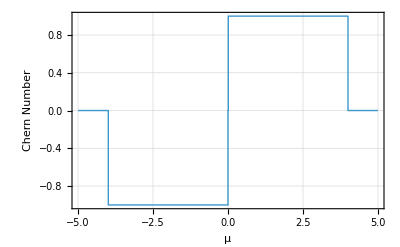

```mathematica
dvec[kx_,ky_,mu_]:={DeltaE*Sin[kx],DeltaE*Sin[ky],-2*(Cos[kx]+Cos[ky])-mu};


computeChern[mu_]:=Module[{integrand,kx,ky,d,dx,dy},
dx=D[dvec[kx,ky,dA1],kx];
dy=D[dvec[kx,ky,dA1],ky];
integrand[k1_,k2_]:=(d=dvec[k1,k2,mu];
Dot[d,Cross[dx/. {kx->k1,ky->k2},dy/. {kx->k1,ky->k2}]]/(Norm[d]^3));
(1/(4 Pi))*NIntegrate[integrand[k1,k2],{k1,-Pi,Pi},{k2,-Pi,Pi},PrecisionGoal->5,AccuracyGoal->6,Method->"GlobalAdaptive",MaxRecursion->20]];

(*Sweep DeltaA1 from 0 to 2.0*)
dA1Values=Range[-5,5,0.01];
chernResults=ParallelTable[{val,Round[computeChern[val]]},{val,dA1Values}];

(*Plotting*)
ListLinePlot[chernResults,InterpolationOrder->0,(*Makes it look like a proper step function*)PlotStyle->Thick,Frame->True,FrameLabel->{"μ","Chern Number"},PlotRange->All,GridLines->Automatic]
```

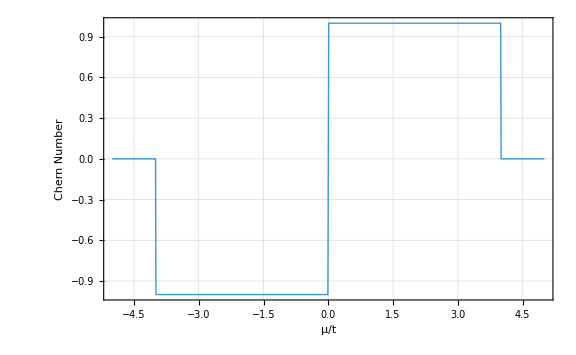

```mathematica
ListLinePlot[chernResults,PlotRange->All,Frame->True,FrameLabel->{Style["μ/t",20,FontFamily->"Times New Roman"],Style["Chern Number",20,FontFamily->"Times New Roman"]},FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->Directive[18,FontFamily->"Times New Roman"],PlotStyle->Thick,ImageSize->Large,GridLines->Automatic]
```